```mathematica
Wcat[α_,x_,p_,s_]:=(ⅇ^(-(x-√2 α)^2-p^2)+ⅇ^(-(x+√2 α)^2-p^2)+s 2 ⅇ^(-x^2-p^2)Cos[2 √2 α p])/(2π(1+s ⅇ^(-2 α^2)));(* Typo in https://arxiv.org/pdf/2006.16985.pdf Eq. (27) *)
```

[Calc] Deriving this Wigner distribution using linearity of Wigner transform in density operators

W1ecat  = 1/Norm[W_(α,Coh.)+W_(-α ,Coh.)+W_(+-)+W_(-+)]

W_(+-)=1/(2π)∫_(-∞)^∞ ⅇ^-ⅈpy ψ_α(x-y/2) ψ_-α*(x+y/2) ⅆy (Wikipedia convention, Gerry and Knight convention)

```mathematica
ψ[x0_,p0_,x_]:=1/π^(1/4)ⅇ^(ⅈ p0 x)ⅇ^((-(x- x0)^2)/2)ⅇ^(-(ⅈ x0 p0)/2); (* Coherent state wave function *)
Wcoh[α_,x_,p_]=1/(2π)∫_(-∞)^∞ ⅇ^(-ⅈ p y)ψ[√2 α,0,x-y/2]ψ[√2 α,-0,x+y/2]ⅆy
Wpm[α_,x_,p_]=1/(2π)∫_(-∞)^∞ ⅇ^(-ⅈ p y)ψ[√2 α,0,x-y/2]ψ[-√2 α,-0,x+y/2]ⅆy
```

(ⅇ^(-p^2-x^2+2 √2 x α-2 α^2))/π

(ⅇ^(-p^2-x^2+2 ⅈ √2 p α))/π

```mathematica
FullSimplify[(Wpm[α,x,p]+Wpm[-α,x,p])]
```

(2 ⅇ^(-p^2-x^2) Cos[2 √2 p α])/π

#### [Calc] Finding the Wigner distribution after homodyne heralding

```mathematica
(* 
   For the current example, Wigner distribution has a form: W^(2)=1/𝒩(W_(++)+W_(--)+W_(+-)+W_(-+)).
First, we are interested in finding W_(++,--,+-,--) separately.

 Careful about using the wavefunction for coherent state here. Imaginary part ⅈrα is important.
 For conjugate: use ψ*(x0,p0;x)-> ψ(x0,-p0;x)
*)
1/(2π)^2∫_(-∞)^∞ ∫_(-∞)^∞ ψ[s1 √2 t α,-0,x1+y1/2]ψ[0,-s1 √2 r α,x2+y2/2]ψ[s2 √2 t α,0,x1-y1/2]ψ[0,s2 √2 r α,x2-y2/2] ⅇ^(-ⅈ p1 y1 -ⅈ p2 y2)ⅆy2ⅆy1
```

(ⅇ^(-p1^2-p2^2-x1^2-x2^2-√2 p2 r (s1+s2) α-ⅈ √2 p1 (s1-s2) t α+√2 (s1+s2) t x1 α-ⅈ √2 r (s1-s2) x2 α-1/2 (s1+s2)^2 (r^2+t^2) α^2))/π^2

```mathematica
(* Simplifying the exponent *)
Collect[FullSimplify[(-2 p1^2-2 p2^2-2 x1^2-2 x2^2+2 √2 p2 r (s1+s2) α-2 ⅈ √2 p1 (s1-s2) t α+2 √2 s1 t x1 α+2 √2 s2 t x1 α+2 ⅈ √2 r s1 x2 α-2 ⅈ √2 r s2 x2 α-r^2 s1^2 α^2-2 r^2 s1 s2 α^2-r^2 s2^2 α^2-s1^2 t^2 α^2-2 s1 s2 t^2 α^2-s2^2 t^2 α^2),(s1|s2)∈{0,1}],{x1,x2,p1,p2}]
```

-2 p1^2-2 p2^2-2 x1^2-2 x2^2+2 √2 p2 r (s1+s2) α-2 ⅈ √2 p1 (s1-s2) t α+2 √2 (s1+s2) t x1 α+2 ⅈ √2 r (s1-s2) x2 α-(s1+s2)^2 (r^2+t^2) α^2

```mathematica
Ws1s2[s1_,s2_]:=Exp[1/2(-2 p1^2-2 p2^2-2 x1^2-2 x2^2+2 √2 p2 r (s1+s2) α-2 ⅈ √2 p1 (s1-s2) t α+2 √2 (s1+s2) t x1 α+2 ⅈ √2 r (s1-s2) x2 α-(s1+s2)^2 (r^2+t^2) α^2)];
```

```mathematica
FullSimplify[Ws1s2[1,1]+Ws1s2[-1,-1]]
```

ⅇ^(-p1^2-p2^2-x1^2-x2^2-2 √2 p2 r α-2 α (√2 t x1+r^2 α+t^2 α)) (1+ⅇ^(4 √2 (p2 r+t x1) α))

```mathematica
W2mode=1/(2 π^2(1+ⅇ^(-2 α^2)))(FullSimplify[Ws1s2[1,1]+Ws1s2[-1,-1]]+FullSimplify[Ws1s2[1,-1]+Ws1s2[-1,+1]])
```

```mathematica
(* Simplifying the numerator *)
FullSimplify[FullSimplify[Ws1s2[1,1]+Ws1s2[-1,-1]]+FullSimplify[Ws1s2[1,-1]+Ws1s2[-1,+1]],{r^2+t^2==1}]
```

ⅇ^(-p1^2-p2^2-x1^2-x2^2-2 √2 p2 r α-2 α (√2 t x1+α)) (1+ⅇ^(4 √2 (p2 r+t x1) α)+2 ⅇ^(2 α (√2 p2 r+√2 t x1+α)) Cos[2 √2 (p1 t-r x2) α])

```mathematica
(* Two-mode Wigner distribution just before heralding *)
W2mode=(ⅇ^(-p1^2-p2^2-x1^2-x2^2-2 √2 p2 r α-2 α (√2 t x1+α)) (1+ⅇ^(4 √2 (p2 r+t x1) α)+2 ⅇ^(2 α (√2 p2 r+√2 t x1+α)) Cos[2 √2 (p1 t-r x2) α]))/(2 (1+ⅇ^(-2 α^2)) π^2);
```

```mathematica
∫_(-∞)^∞ ⅇ^(-p1^2-p2^2-x1^2-x2^2-2 √2 p2 r α-2 α (√2 t x1+α)) (1+ⅇ^(4 √2 (p2 r+t x1) α)+2 ⅇ^(2 α (√2 p2 r+√2 t x1+α)) Cos[2 √2 (p1 t-r x2) α])ⅆp2
```

ⅇ^(-p1^2-x1^2-x2^2-2 √2 t x1 α) √π (ⅇ^(2 (-1+r^2) α^2) (1+ⅇ^(4 √2 t x1 α))+2 ⅇ^(2 √2 t x1 α) Cos[2 √2 (p1 t-r x2) α])

```mathematica
FullSimplify[ⅇ^(-p1^2-x1^2-x2^2-2 √2 t x1 α) √π (ⅇ^(2 (-1+r^2) α^2) (1+ⅇ^(4 √2 t x1 α))+2 ⅇ^(2 √2 t x1 α) Cos[2 √2 (p1 t-r x2) α]),{r^2+t^2==1}]
```

ⅇ^(-p1^2-x1^2-x2^2-2 √2 t x1 α-2 t^2 α^2) √π (1+ⅇ^(4 √2 t x1 α)+2 ⅇ^(2 t α (√2 x1+t α)) Cos[2 √2 (p1 t-r x2) α])

```mathematica
(* After tracing out the momentum in mode 2 *)
Wbh = 1/(π^2 2(1+ⅇ^(-2 α^2)))ⅇ^(-p1^2-x1^2-x2^2-2 √2 t x1 α-2 t^2 α^2) √π (1+ⅇ^(4 √2 t x1 α)+2 ⅇ^(2 t α (√2 x1+t α)) Cos[2 √2 (p1 t-r x2) α]);
Wbhnumer[α_,x1_,p1_,x2_,t_,r_]:=ⅇ^(-p1^2-x1^2-x2^2-2 √2 t x1 α-2 t^2 α^2) √π (1+ⅇ^(4 √2 t x1 α)+2 ⅇ^(2 t α (√2 x1+t α)) Cos[2 √2 (p1 t-r x2) α])
```

[Calc] To check if the two-mode Wigner (w/o heralding), normalizes to 1

```mathematica
ClearAll[t,r,α,Δ]
```

```mathematica
∫_(-∞)^∞ Wbhnumer[α,x1,p1,x2,t,r]ⅆx2
```

```mathematica
FullSimplify[ⅇ^(-p1^2-x1^2-2 √2 t x1 α-2 (r^2+t^2) α^2) π (ⅇ^(2 r^2 α^2) (1+ⅇ^(4 √2 t x1 α))+2 ⅇ^(2 t α (√2 x1+t α)) Cos[2 √2 p1 t α]),{r^2+t^2==1}]
```

ⅇ^(-p1^2-x1^2-2 √2 t x1 α-2 α^2) π (ⅇ^(2 r^2 α^2) (1+ⅇ^(4 √2 t x1 α))+2 ⅇ^(2 t α (√2 x1+t α)) Cos[2 √2 p1 t α])

```mathematica
∫_(-∞)^∞ ⅇ^(-p1^2-x1^2-2 √2 t x1 α-2 α^2) π (ⅇ^(2 r^2 α^2) (1+ⅇ^(4 √2 t x1 α))+2 ⅇ^(2 t α (√2 x1+t α)) Cos[2 √2 p1 t α])ⅆp1
```

ⅇ^(-x1^2-2 √2 t x1 α-2 α^2) (2 ⅇ^(2 √2 t x1 α)+ⅇ^(2 r^2 α^2)+ⅇ^(2 α (2 √2 t x1+r^2 α))) π^(3/2)

```mathematica
FullSimplify[ⅇ^(-x1^2-2 √2 t x1 α-2 α^2) (2 ⅇ^(2 √2 t x1 α)+ⅇ^(2 r^2 α^2)+ⅇ^(2 α (2 √2 t x1+r^2 α))) π^(3/2),{r^2+t^2==1}]
```

ⅇ^(-x1^2-2 √2 t x1 α-2 α^2) (2 ⅇ^(2 √2 t x1 α)+ⅇ^(2 r^2 α^2)+ⅇ^(2 α (2 √2 t x1+r^2 α))) π^(3/2)

```mathematica
FullSimplify[1/(π^2 2(1+ⅇ^(-2 α^2)))∫_(-∞)^∞ ⅇ^(-x1^2-2 √2 t x1 α-2 α^2) (2 ⅇ^(2 √2 t x1 α)+ⅇ^(2 r^2 α^2)+ⅇ^(2 α (2 √2 t x1+r^2 α))) π^(3/2)ⅆx1,{r^2+t^2==1}]
```

1

[Calc] Heralding on Δ range in x_2 around the origin

```mathematica
(* We are leaving out the normalization 𝒩 in the denominator for now and focus on the numerator only. *)
∫_(-Δ/2)^(Δ/2) Wbhnumer[α,x1,p1,x2,t,r]ⅆx2
```

```mathematica
FullSimplify[ⅇ^(-p1^2-x1^2-2 √2 t x1 α-2 (r^2+t^2) α^2) π (ⅇ^(2 r^2 α^2) (1+ⅇ^(4 √2 t x1 α)) Erf[Δ/2]+ⅈ ⅇ^(2 t α (√2 x1+t α)) Cos[2 √2 p1 t α] (Erfi[√2 r α-(ⅈ Δ)/2]-Erfi[√2 r α+(ⅈ Δ)/2])),{r^2+t^2==1}]
```

ⅇ^(-p1^2-x1^2-2 √2 t x1 α-2 α^2) π (ⅇ^(2 r^2 α^2) (1+ⅇ^(4 √2 t x1 α)) Erf[Δ/2]+ⅈ ⅇ^(2 t α (√2 x1+t α)) Cos[2 √2 p1 t α] (Erfi[√2 r α-(ⅈ Δ)/2]-Erfi[√2 r α+(ⅈ Δ)/2]))

```mathematica
Wh[α_,x1_,p1_,Δ_,t_,r_]:=ⅇ^(-p1^2-x1^2-2 √2 t x1 α-2 α^2) π (ⅇ^(2 r^2 α^2) (1+ⅇ^(4 √2 t x1 α)) Erf[Δ/2]+ⅈ ⅇ^(2 t α (√2 x1+t α)) Cos[2 √2 p1 t α] (Erfi[√2 r α-(ⅈ Δ)/2]-Erfi[√2 r α+(ⅈ Δ)/2]))/(π^2 2(1+ⅇ^(-2 α^2)));
```

```mathematica
∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(-p1^2-x1^2-2 √2 t x1 α-2 α^2) π (ⅇ^(2 r^2 α^2) (1+ⅇ^(4 √2 t x1 α)) Erf[Δ/2]+ⅈ ⅇ^(2 t α (√2 x1+t α)) Cos[2 √2 p1 t α] (Erfi[√2 r α-(ⅈ Δ)/2]-Erfi[√2 r α+(ⅈ Δ)/2]))ⅆx1ⅆp1
```

ⅇ^(-2 α^2) π^2 (2 ⅇ^(2 (r^2+t^2) α^2) Erf[Δ/2]+ⅈ (Erfi[√2 r α-(ⅈ Δ)/2]-Erfi[√2 r α+(ⅈ Δ)/2]))

#### [Rslt] Wigner distributions - essential code

```mathematica
Wh[α_,x1_,p1_,Δ_,t_,r_]:=ⅇ^(-p1^2-x1^2-2 √2 t x1 α-2 α^2) π (ⅇ^(2 r^2 α^2) (1+ⅇ^(4 √2 t x1 α)) Erf[Δ/2]+ ⅇ^(2 t α (√2 x1+t α)) Cos[2 √2 p1 t α] 2 Im[Erfi[√2 r α+(ⅈ Δ)/2]])/(π^2 2(1+ⅇ^(-2 α^2)));Ps[α_,Δ_,t_,r_]:= (ⅇ^(-2 α^2) π^2 (2 ⅇ^(2 (r^2+t^2) α^2) Erf[Δ/2]+2Im[Erfi[√2 r α+(ⅈ Δ)/2]]))/(2 π^2(1+ⅇ^(-2 α^2)));

WhnHomodyne[α_,x1_,p1_,Δ_,t_]:=Re[Wh[α,x1,p1,Δ,t,√(1-t^2)]/Ps[α,Δ,t,√(1-t^2)]];
Wcat[α_,x_,p_,s_]:=(ⅇ^(-(x-√2 α)^2-p^2)+ⅇ^(-(x+√2 α)^2-p^2)+s 2 ⅇ^(-x^2-p^2)Cos[2 √2 α p])/(2π(1+s ⅇ^(-2 α^2)));(* Typo in https://arxiv.org/pdf/2006.16985.pdf Eq. (27) *)

(* Results for the threshold detectors obtained from Appendix of the paper: https://doi.org/10.1103/PhysRevA.105.013704 *)
WhnThreshold[α_,x1_,p1_,η_,t_]:=((Cosh[t^2 α^2]Cosh[(1-η)(1-t^2)α^2])/Cosh[α^2(1-η (1-t^2))])Wcat[t α,x1,p1,1]+((Sinh[t^2 α^2]Sinh[(1-η)(1-t^2)α^2])/Cosh[α^2(1-η (1-t^2))])Wcat[t α,x1,p1,-1];
```

#### Fixing Δ finding η

0.190839

{η→0.98}

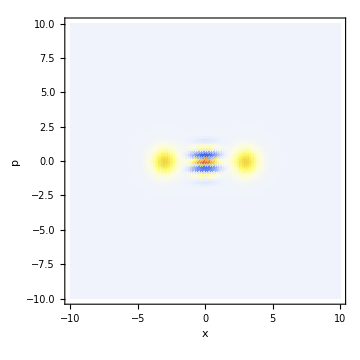
(a) Threshold | (b) Homodyne
-Graphics- | -Graphics-

```mathematica
ClearAll[η,Δ,model, fit,Data,IdxData, limits, range];
limits=10;
range=55;
α=3;
Δ=0.3415093003830734;
t =√0.5;(* This is the beamsplitter transmittivity of the beamsplitter used for ZPS *)
Re[Ps[α,Δ,t,√(1-t^2)]](* Psuccess *)
matWhHomodyne=Table[Re[Chop[WhnHomodyne[α,(x-1)(limits/range)-limits,(p-1)(limits/range)-limits,Δ,t]]],{p,1,2 range +1},{x,1,2 range +1}];
matWhHomodyne =matWhHomodyne/(Total[matWhHomodyne,2](limits/range)^2);

model=WhnThreshold[α,x,p,η,t];
range =(Dimensions[matWhHomodyne][[1]]-1)/2;
IdxData= Table[{(i-range -1)limits/range,(j-range-1)limits/range,matWhHomodyne[[i,j]]},{i,1,2range+1},{j,1,2range+1}];
Data=Flatten[IdxData,1];
fit = FindFit[Data,model,{{η,0.5}},{p,x}]


matWhThreshold=Table[Re[Chop[WhnThreshold[α,(x-1)(limits/range)-limits,(p-1)(limits/range)-limits,η/.fit,t]]],{p,1,2 range +1},{x,1,2 range +1}];
matWhThreshold = matWhThreshold/(Total[matWhThreshold,2](limits/range)^2);

plotThreshold=ListDensityPlot[matWhThreshold,DataRange->{{-limits,limits},{-limits,limits}},ColorFunction->"TemperatureMap",ColorFunctionScaling->True,PlotRange->All,AxesLabel->{x,p},LabelStyle->{FontSize->Medium,FontFamily->"Arial",Black},AxesStyle->{Thick,Black},ImageSize->Medium];
plotHomodyne=ListDensityPlot[matWhHomodyne,DataRange->{{-limits,limits},{-limits,limits}},ColorFunction->"TemperatureMap",ColorFunctionScaling->True,PlotRange->All,AxesLabel->{x,p},LabelStyle->{FontSize->Medium,FontFamily->"Arial",Black},AxesStyle->{Thick,Black},ImageSize->Medium];
Grid[{{"(a) Threshold","(b) Homodyne"},{plotThreshold,plotHomodyne}}]
```

```mathematica
ClearAll[η,Δ,model, fit,Data,IdxData,α,plotvalues,plots, limits, range];
limits=10;
range=55;
t =√0.5;(* This is the beamsplitter transmittivity of the beamsplitter used for ZPS *)

{Δmin,Δmax,dΔ}={0.01,1,0.05};
{αmin,αmax,dα}={1,5,1};

plots={};
Monitor[
Do[
plotvalues[{α,t}]={};
Do[
matWhHomodyne=Table[Re[Chop[WhnHomodyne[α,(x-1)(limits/range)-limits,(p-1)(limits/range)-limits,Δ,t]]],{p,1,2 range +1},{x,1,2 range +1}];
matWhHomodyne = matWhHomodyne/(Total[matWhHomodyne,2](limits/range)^2);
model=WhnThreshold[α,x,p,η,t];
     range =(Dimensions[matWhHomodyne][[1]]-1)/2;
IdxData= Table[{(i-range -1)limits/range,(j-range-1)limits/range,matWhHomodyne[[i,j]]},{i,1,2range+1},{j,1,2range+1}];
Data=Flatten[IdxData,1];
fit = FindFit[Data,model,η,{p,x}];
AppendTo[plotvalues[{α,t}],{Δ,η/.fit}]
,{Δ,Δmin,Δmax,dΔ}];
AppendTo[plots,plotvalues[{α,t}]]
,{α,αmin,αmax,dα}],
{ProgressIndicator[Dynamic[Δ/Δmax]],
ProgressIndicator[Dynamic[α/αmax]]}]
```

```mathematica
Dimensions[plots[[1;;3]]]
```

{3,20,2}

```mathematica
plot1=ListLinePlot[plots[[1;;3]],AxesLabel->{"Δ","η"},LabelStyle->{FontSize->20,FontFamily->"Arial",Black},AxesStyle->{{Thick,Black},{Thick,Black}},ImageSize->Medium,PlotRange->Full];
plot2 = ListLinePlot[plots[[4,1;;16]],AxesLabel->{"Δ","η"},LabelStyle->{FontSize->20,FontFamily->"Arial",Black},AxesStyle->{{Thick,Black},{Thick,Black}},ImageSize->Medium,PlotRange->Full,PlotStyle->Red];
plot3 = ListLinePlot[plots[[5,1;;13]],AxesLabel->{"Δ","η"},LabelStyle->{FontSize->20,FontFamily->"Arial",Black},AxesStyle->{{Thick,Black},{Thick,Black}},ImageSize->Medium,PlotRange->Full,PlotStyle->Purple];
Show[{plot1,plot2,plot3}]
```

```mathematica
ListLinePlot[plots,AxesLabel->{"Δ","η"},LabelStyle->{FontSize->20,FontFamily->"Arial",Black},AxesStyle->{{Thick,Black},{Thick,Black}},ImageSize->Medium,PlotRange->Full]
```

Results

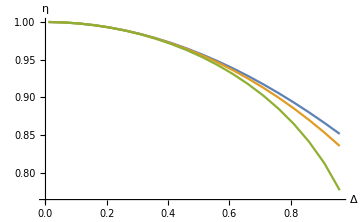

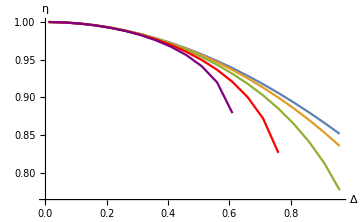

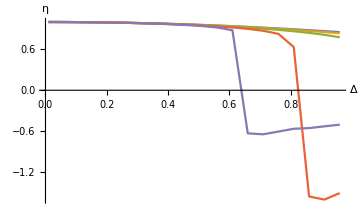

#### Fixing η finding Δ (this way is difficult and the results don’t match for large α. Possible reason: FindFit function is trying to fit a much more complicated model, involving Erf and Erfi functions instead of simple Gaussian and cosines)

```mathematica
ClearAll[η,Δ,model, fit,Data,IdxData,α,plotvalues,plots, limits, range];
limits=10;
range=55;
t =√0.5;(* This is the beamsplitter transmittivity of the beamsplitter used for ZPS *)

{ηmin,ηmax,dη}={0.1,0.9,0.1};
{αmin,αmax,dα}={1,5,1};

plots2={};
Monitor[Do[
plotvalues[{α,t}]={};
Do[
matWhThreshold=Table[Re[Chop[WhnThreshold[α,(x-1)(limits/range)-limits,(p-1)(limits/range)-limits,η,t]]],{p,1,2 range +1},{x,1,2 range +1}];
matWhThreshold = matWhThreshold/(Total[matWhThreshold,2](limits/range)^2);
model=WhnHomodyne[α,x,p,Δ,t];
range =(Dimensions[matWhThreshold][[1]]-1)/2;
IdxData= Table[{(i-range -1)limits/range,(j-range-1)limits/range,matWhThreshold[[i,j]]},{i,1,2range+1},{j,1,2range+1}];
Data=Flatten[IdxData,1];
fit = FindFit[Data,model,Δ,{p,x}];
AppendTo[plotvalues[{α,t}],{η,Δ/.fit}]
,{η,ηmin,ηmax,dη}];
AppendTo[plots2,plotvalues[{α,t}]]
,{α,αmin,αmax,dα}],
,
{ProgressIndicator[Dynamic[η/ηmax]],
ProgressIndicator[Dynamic[α/αmax]]}]
```

```mathematica
ListLinePlot[plots2,AxesLabel->{"η","Δ"},LabelStyle->{FontSize->20,FontFamily->"Arial",Black},InterpolationOrder->2,AxesStyle->{{Thick,Black},{Thick,Black}},ImageSize->Medium,PlotRange->Full]
```

```mathematica
ClearAll[η,Δ,model, fit,Data,IdxData];
limits=10;
range=55;
α=3;
η=0.98;
t =√0.5;(* This is the beamsplitter transmittivity of the beamsplitter used for ZPS *)

matWhThreshold=Table[Re[Chop[WhnThreshold[α,(x-1)(limits/range)-limits,(p-1)(limits/range)-limits,η,t]]],{p,1,2 range +1},{x,1,2 range +1}];
matWhThreshold = matWhThreshold/(Total[matWhThreshold,2](limits/range)^2);


model=WhnHomodyne[α,x,p,Δ,t];
range =(Dimensions[matWhThreshold][[1]]-1)/2;
IdxData= Table[{(i-range -1)limits/range,(j-range-1)limits/range,matWhThreshold[[i,j]]},{i,1,2range+1},{j,1,2range+1}];
Data=Flatten[IdxData,1];
fit = FindFit[Data,model,Δ,{p,x}]

Re[Ps[α,Δ/.fit,t,√(1-t^2)]](* Psuccess *)
matWhHomodyne=Table[Re[Chop[WhnHomodyne[α,(x-1)(limits/range)-limits,(p-1)(limits/range)-limits,Δ/.fit,t]]],{p,1,2 range +1},{x,1,2 range +1}];
matWhHomodyne =matWhHomodyne/(Total[matWhHomodyne,2](limits/range)^2);

matWhThreshold=Table[Re[Chop[WhnThreshold[α,(x-1)(limits/range)-limits,(p-1)(limits/range)-limits,η/.fit,t]]],{p,1,2 range +1},{x,1,2 range +1}];

plotThreshold=ListDensityPlot[matWhThreshold,DataRange->{{-limits,limits},{-limits,limits}},ColorFunction->"TemperatureMap",ColorFunctionScaling->True,PlotRange->All,AxesLabel->{x,p},LabelStyle->{FontSize->Medium,FontFamily->"Arial",Black},AxesStyle->{Thick,Black},ImageSize->Medium];
plotHomodyne=ListDensityPlot[matWhHomodyne,DataRange->{{-limits,limits},{-limits,limits}},ColorFunction->"TemperatureMap",ColorFunctionScaling->True,PlotRange->All,AxesLabel->{x,p},LabelStyle->{FontSize->Medium,FontFamily->"Arial",Black},AxesStyle->{Thick,Black},ImageSize->Medium];
Grid[{{"(a) Threshold","(b) Homodyne"},{plotThreshold,plotHomodyne}}]
```

{Δ→0.341509}

0.190839

(a) Threshold | (b) Homodyne
-Graphics- | -Graphics-

#### [Calc] Coefficient of the interference term

```mathematica
ClearAll[α,t,r];
Simplify[Expand[Simplify[(cp Wcat[t α,x1,p1,1]+cm Wcat[t α,x1,p1,-1])]]]
```

(ⅇ^(-p1^2-2 (x1^2+t^2 α^2)) ((cm+cp) (ⅇ^((x1-√2 t α)^2)+ⅇ^((x1+√2 t α)^2))-2 (cm-cp) ⅇ^(x1^2+4 t^2 α^2) Cos[2 √2 p1 t α]))/(2 (1+ⅇ^(2 t^2 α^2)) π)

```mathematica
(* General *)
FringeTerm=FullSimplify[ (ⅇ^(-p1^2-2 (x1^2+t^2 α^2))2 (-1+2 cp) ⅇ^(x1^2+4 t^2 α^2))/(2 (1+ⅇ^(2 t^2 α^2)) π)]
```

((-1+2 cp) ⅇ^(-p1^2-x1^2) (1+Tanh[t^2 α^2]))/(2 π)

```mathematica
ClearAll[Δ];
FringeTermHomodyne=FullSimplify[(ⅇ^(-p1^2-x1^2-2 √2 t x1 α-2 α^2)  π ⅇ^(2 t α (√2 x1+t α))2 Im[Erfi[√2 r α+(ⅈ Δ)/2]])/(ⅇ^(-2 α^2) π^2 (2 ⅇ^(2  α^2) Erf[Δ/2]+2Im[Erfi[√2 r α+(ⅈ Δ)/2]]))]
```

(ⅇ^(-p1^2-x1^2+2 t^2 α^2) Im[Erfi[√2 r α+(ⅈ Δ)/2]])/(ⅇ^(2 α^2) π Erf[Δ/2]+π Im[Erfi[√2 r α+(ⅈ Δ)/2]])

#### Observations

-For large α, and low η it seems Δ doesn’t exist
-For  Δ > Δ_m, η doesn’t exist 
-We are projecting on infinitely squeezed states with arbitrary momentum coordinate. Does this mean ‘n’ can take high values too and so we are not heralding on zero photons?

#### Next Steps

Add the Psuccess for threshold detectors in the comparison as well .